```mathematica
<<"/Users/xiyin/Dropbox/string theory/ConformalBlock.m";
prec = 100;

(*** elliptic nome q(z) as defined in (D.100) ***)
nomeQ[z_] := E^(-π EllipticK[1-z]/EllipticK[z]);

(*** application of recusion formulae requires rationalizing numerical values of weights and central charge ***)
RationPrec[f_]:=Rationalize[f,10^(-prec)]

(*** converting Liouville momentum p to holomorphic weight h ***)
weight[p_]:=Q^2/4+p^2;

(*** central charge of Liouville theory, c=25 as in the application to c=1 string theory; slight deviation from 25 is necessary for the recusive representation to be non-singular ***)
c=25.00001//RationPrec;

(*** background charge Q and the parameter b ***)
b=RationPrec[(bb/.Solve[1+6(bb+1/bb)^2==c,bb])[[4]]//N];
Q=RationPrec[b+1/b];

UpsilonIntegrand[bb_,x_]=1/t*(1/4 ⅇ^-t (1/bb+bb-2 x)^2-ⅇ^(-t x)((1-ⅇ^(-t (1/2 (1/bb+bb)-x)))^2)/((1-ⅇ^(-t/bb)) (1-ⅇ^(-bb t))));

(*** Subscript[Υ, b](x) function as defined in (H.56) ***)
Upsilon[bb_,x_]:=Exp[NIntegrate[UpsilonIntegrand[bb,x],{t,0,Infinity},MaxRecursion->1000,Method->{"LevinRule", TimeConstraint->1000}]]

(*** DOZZ structure constant (H.58) with the constant factor Subscript[Υ, b]'(0) stripped off ***)
DOZZ[bb_,p1_,p2_,p3_]:=1/Upsilon[bb,(bb+1/bb)/2+I(p1+p2+p3)]*Sqrt[Upsilon[bb,2 I p1] Upsilon[bb,-2 I p1]]/Upsilon[bb,(bb+1/bb)/2+I(p1+p2+p3)-2I p1]*Sqrt[Upsilon[bb,2 I p2] Upsilon[bb,-2 I p2]]/Upsilon[bb,(bb+1/bb)/2+I(p1+p2+p3)-2I p2]*Sqrt[Upsilon[bb,2 I p3] Upsilon[bb,-2 I p3]]/Upsilon[bb,(bb+1/bb)/2+I(p1+p2+p3)-2I p3]

(*** An equivalent expression of the DOZZ structure constant in the special case c=25 that is manifestly analytic in p1, p2, p3, as in (4.119) ***)
DOZZc25[p1_,p2_,p3_]:=1/Upsilon[1,1+I(p1+p2+p3)]*(2 p1 Upsilon[1,1+2I p1])/Upsilon[1,1+I(p1+p2+p3)-2I p1]*(2 p2 Upsilon[1,1+2I p2])/Upsilon[1,1+I(p1+p2+p3)-2I p2]*(2 p3 Upsilon[1,1+2I p3])/Upsilon[1,1+I(p1+p2+p3)-2I p3]
```

```mathematica
VirasoroBlock[{h1_,h2_,h3_,h4_},hint_,z_,TruncationOrder_]:=S4CBq[TruncationOrder,h1,h2,h3,h4,hint,c,z,nomeQ[z]]

(*** 4-point correlator as in (H.42) ***)
LiouvilleIntegrand[{np1_,np2_,np3_,np4_},npint_,z_,TruncationOrder_]:=Module[{p1,p2,p3,p4,pint},{p1,p2,p3,p4,pint}={np1,np2,np3,np4,npint}//RationPrec;1/Pi * DOZZ[b,p1,p2,pint] * DOZZ[b,p3,p4,pint] * VirasoroBlock[{weight[p1],weight[p2],weight[p3],weight[p4]},weight[pint],z,TruncationOrder] * VirasoroBlock[{weight[p1],weight[p2],weight[p3],weight[p4]},weight[pint],Conjugate[z],TruncationOrder]]

(*** "prange" is the range of integration over internal Liouville momenta, with step size "step". TruncationOrder is the order of truncation in the q-expansion of the Virasoro conformal block ***)
Correlator[{p1_,p2_,p3_,p4_},z_,prange_,step_,TruncationOrder_]:=Module[{pint,func,y,NumericalIntegrand},NumericalIntegrand=Monitor[Table[{pint,LiouvilleIntegrand[{p1,p2,p3,p4},pint,z,TruncationOrder]},{pint,step,prange,step}],pint];
func=Interpolation[NumericalIntegrand];
NIntegrate[func[y],{y,0,prange}]]
```

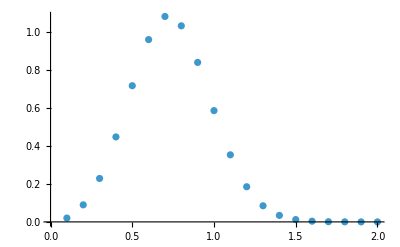

```mathematica
(*** getting a sense of the distribution of integrand in internal Liouville momentum P = pint, in the case where external Liouville momenta are set to {.3,.3,.3,.3}, and cross ratio z = 0.8 ***)
NumericalIntegrand=Monitor[Table[{pint,LiouvilleIntegrand[{.3,.3,.3,.3},pint,.8,5]},{pint,1/10,2,1/10}],pint];
ListPlot[NumericalIntegrand]
```

```mathematica
(*** Liouville CFT 4-point function with external Liouville momenta p1=p2=p3=p4=0.3, cross ratio z=0.2 ***)
(*** for relatively small value of z, truncation order 5 in the q-expansion is sufficient ***)
Correlator[{.3,.3,.3,.3},.2,2,.01,5]
```

0.622744

```mathematica
(*** the same correlator in the cross channel related by z->1-z ***)
(*** for cross ratio z=0.8, need to go to higher truncation orders in the q-expansion for accurate result ***)
Correlator[{.3,.3,.3,.3},.8,2,.01,5]
Correlator[{.3,.3,.3,.3},.8,2,.01,7]
Correlator[{.3,.3,.3,.3},.8,2,.01,10]
```

0.669027

0.626273

0.622666

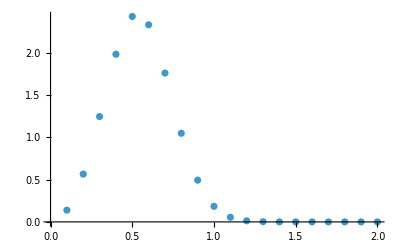

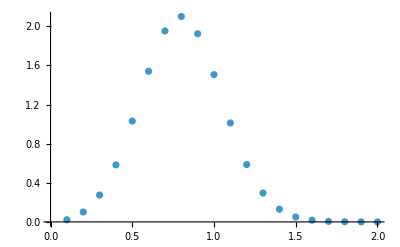

```mathematica
(*** an example with distinct external Liouville momenta ***)
NumericalIntegrand=Monitor[Table[{pint,LiouvilleIntegrand[{.21,.33,.4,.52},pint,.2,5]},{pint,1/10,2,1/10}],pint];
ListPlot[NumericalIntegrand]

(*** cross channel related by z->1-z and swapping p2, p3 ***)
NumericalIntegrand=Monitor[Table[{pint,LiouvilleIntegrand[{.21,.4,.33,.52},pint,.8,5]},{pint,1/10,2,1/10}],pint];
ListPlot[NumericalIntegrand]
```

```mathematica
Correlator[{.21,.33,.4,.52},.2,2,.01,5]
```

1.22404

```mathematica
(*** cross channel, with p2 and p3 swapped ***)
Correlator[{.21,.4,.33,.52},.8,2,.01,5]
Correlator[{.21,.4,.33,.52},.8,2,.01,7]
Correlator[{.21,.4,.33,.52},.8,2,.01,10]
```

1.31305

1.2309

1.2239